```mathematica
F[m_, k_, r_] = Boole[m>k*r]
```

Boole[m>k r]

```mathematica
F[1, 0.2, 2]
```

1

```mathematica
PDF[PoissonDistribution[z],k]
```

Piecewise[{{(ⅇ^-z z^k)/(k!), k≥0}, {0, True}}]

```mathematica
PDF[BinomialDistribution[k,q],m]
```

Piecewise[{{(1-q)^(k-m) q^m Binomial[k,m], 0≤m≤k}, {0, True}}]

```mathematica
G[q_, z_, r_] = Sum[PDF[PoissonDistribution[z],k]*k/z*Sum[PDF[BinomialDistribution[k-1,q],m]*Boole[m>k*r], {m, 0, k-1}],{k,1,100}]
```

ⅇ^-z Boole[0>r]+ⅇ^-z z (1)+96+1/154+(ⅇ^-z z^99 ((1-q)^99 Boole[0>100 r]+99 (1-q)^98 q Boole[1>100 r]+97+q^99 Boole[99>100 r]))/(933262154439441526816992388562667004907159682643816214685929638291565182862536979208272237582511852109168640000000000000000000000)
 |  |  |  |

```mathematica
G[0.7, 3, 0.2]
```

0.861368

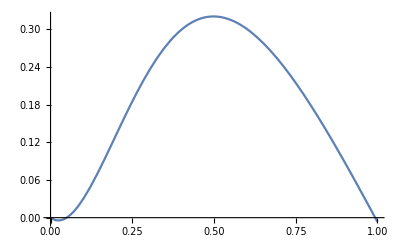

```mathematica
Plot[G[q, 5, 0.2]-q, {q, 0, 1}]
```

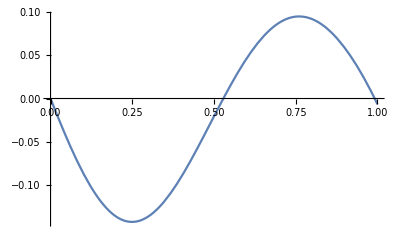

```mathematica
Plot[G[q, 5, 0.4]-q, {q, 0, 1}]
```

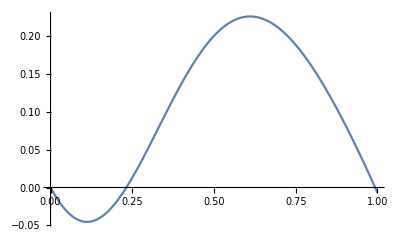

```mathematica
Plot[G[q, 5, 0.3]-q, {q, 0, 1}]
```

```mathematica
.14
```

{q→0.993001}

```mathematica
ρ [ϕ_, q_, z_, r_] = ϕ + (1-ϕ)*( Sum[PDF[PoissonDistribution[z],k]*Sum[PDF[BinomialDistribution[k,q],m]*F[m, k, r], {m, 1, k}],{k,1,100}])
```

ϕ+(1-ϕ) (ⅇ^-z q z F[1,1,r]+1/2 ⅇ^-z z^2 (2 (1-q) q F[1,2,r]+q^2 F[2,2,r])+1/6 ⅇ^1 z^3 (1)+94+1+(ⅇ^-z z^99 (99 (1-q)^98 q F[1,99,r]+97+q^99 F[99,99,r]))/933262154439441526816992388562667004907159682658272237582511852109168640000000000000000000000+(ⅇ^-z z^100 (100 (1-q)^99 q F[1,100,r]+4950 (1-q)^98 q^2 F[2,100,r]+161700 (1-q)^97 q^3 F[3,100,r]+3921225 (1-q)^96 q^4 F[4,100,r]+75287520 (1-q)^95 q^5 F[5,100,r]+90+3921225 (1-q)^4 q^96 F[96,100,r]+161700 (1-q)^3 q^97 F[97,100,r]+4950 (1-q)^2 q^98 F[98,100,r]+100 (1-q) q^99 F[99,100,r]+q^100 F[100,100,r]))/93326215443944152681699238856266700490715968264381621468592963895217599993229915608941463976156518286253697920827223758251185210916864000000000000000000000000)
 |  |  |  |

```mathematica
ρ[0.001, q, 5, 0.3] /.%12
```

0.993029

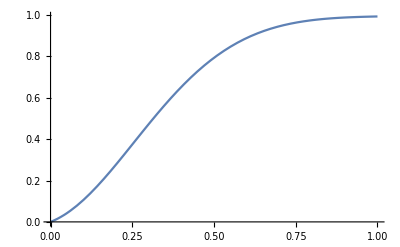

```mathematica
Plot[ρ[0.00, q, 5, 0.3] , {q, 0, 1}]
```

```mathematica
Cascade[r_, z_] = Sum[PDF[PoissonDistribution[z],k]*k*(k-1)*F[1,k, r]/z, {k,1, 1000}]
```

ⅇ^-z z Boole[1>2 r]+ⅇ^-z z^2 Boole[1>3 r]+1+994+(ⅇ^-z z^998 Boole[1])/4035972446164539252600000000000000000+(ⅇ^-z z^999 Boole[1>1000 r])/(402790050127220994538240674597601587306681545756471103647447352437000000000000000000000000000000000000000000000000000000000000000)
 |  |  |  |

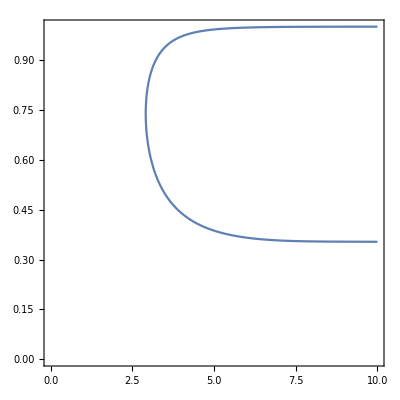

```mathematica
ContourPlot[G[q, z, 0.371]==q , {z, 0, 10},  {q, 0, 1}, MaxRecursion->4]
```

```mathematica
Ggauss[q_, z_, r_] = Sum[PDF[PoissonDistribution[z],k]*k/z*Sum[PDF[BinomialDistribution[k-1,q],m]*CDF[NormalDistribution[r,0.2],m/k], {m, 0, k-1}],{k,1,100}]
```

1/2 ⅇ^-z Erfc[3.53553 r]+ⅇ^-z z (1/2 q Erfc[3.53553 (-1/2+r)]+1/2 (1-q) Erfc[3.53553 r])+1/2 ⅇ^-z z^2 (1/2 q^2 Erfc[3.53553 (-2/3+r)]+(1-q) q Erfc[3.53553 (-1/3+r)]+1/2 (1-q)^2 Erfc[3.53553 r])+94+1/96147000+1+(ⅇ^-z z^99 (1/2 q^99 Erfc[3.53553 (-99/100+r)]+99/2 (1-q) q^98 Erfc[3.53553 (-49/50+r)]+4851/2 (1-q)^2 q^97 Erfc[3.53553 (-97/100+r)]+94+4851/2 (1-q)^97 q^2 Erfc[3.53553 (-1/50+r)]+99/2 (1-q)^98 q Erfc[3.53553 (-1/100+r)]+1/2 (1-q)^99 Erfc[3.53553 r]))/933262154439441526816992388562667004907159682643816214685929638952175999932299156089414639761565182862536979208272237582511852109168640000000000000000000000
 |  |  |  |

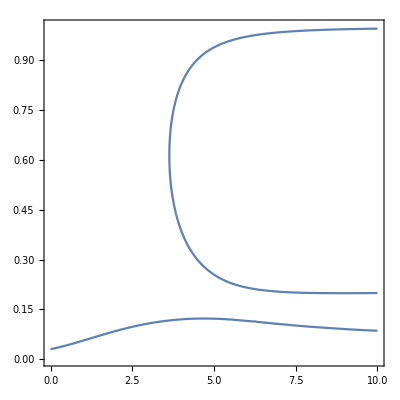

```mathematica
qz375  =ContourPlot[Ggauss[q, z, 0.375]==q , {z, 0, 10},  {q, 0, 1}, MaxRecursion->4]
```

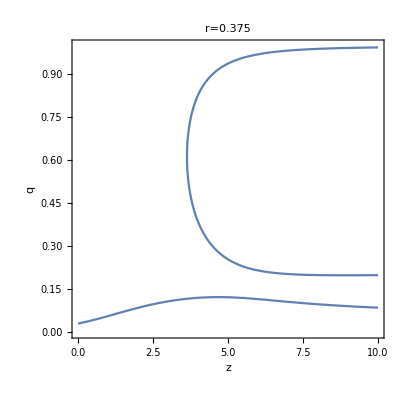

```mathematica
Show[qz375,FrameLabel->{{HoldForm[q],None},{HoldForm[z],None}},PlotLabel->HoldForm[r=0.375],LabelStyle->{GrayLevel[0]}]
```

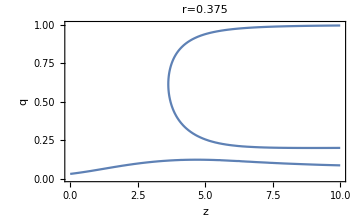

```mathematica
Show[%105,ImageSize->{360,215},AspectRatio->Full]
```

```mathematica
Export["/home/user/Desktop/MP_doc_templates/figures/one_layer_qv_r0375.eps",%106,"EPS"]
```

/home/user/Desktop/MP_doc_templates/figures/one_layer_qv_r0375.eps

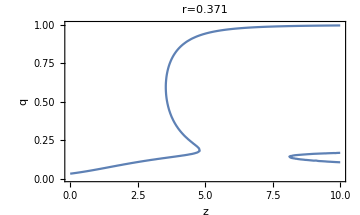

```mathematica
ContourPlot[Ggauss[q, z, 0.371]==q ,  {z, 0, 10},{q, 0, 1}, MaxRecursion->4, AxesLabel->{z,q}, PlotLabel->"r=0.371", ImageSize->{360, 215}, AspectRatio->Full]
```

```mathematica
Show[%108,AxesLabel->{None,None},FrameLabel->{{HoldForm[q],None},{HoldForm[z],None}},PlotLabel->HoldForm[r=0.371],LabelStyle->{GrayLevel[0]}]
```

-Graphics-

```mathematica
Show[%109,ImageSize->{360,215},AspectRatio->Full]
```

-Graphics-

```mathematica
Export["/home/user/Desktop/MP_doc_templates/figures/one_layer_qv_r0371.eps",%110,"EPS"]
```

/home/user/Desktop/MP_doc_templates/figures/one_layer_qv_r0371.eps

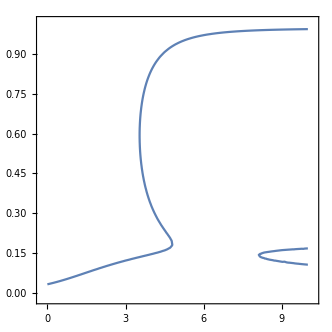

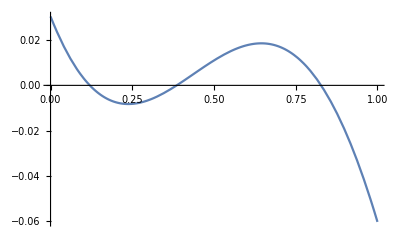

```mathematica
Plot[Ggauss[q, 4, 0.375]-q, {q, 0, 1}]
```

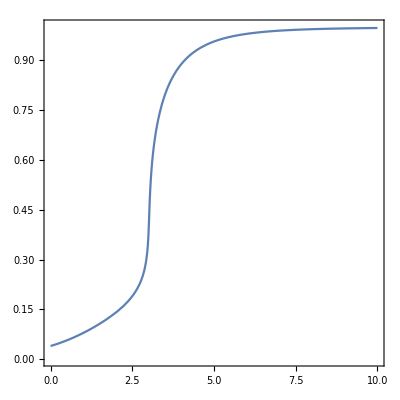

```mathematica
ContourPlot[Ggauss[q, z, 0.35]==q , {z, 0, 10},  {q, 0, 1}, MaxRecursion->4]
```

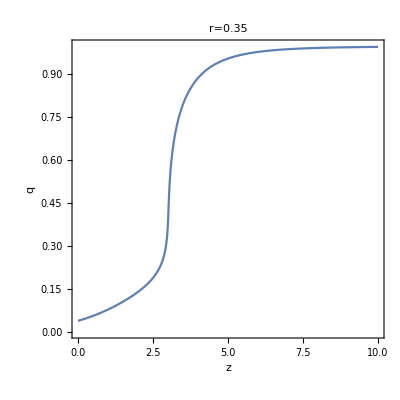

```mathematica
Show[%112,FrameLabel->{{HoldForm[q],None},{HoldForm[z],None}},PlotLabel->HoldForm[r=0.35],LabelStyle->{GrayLevel[0]}]
```

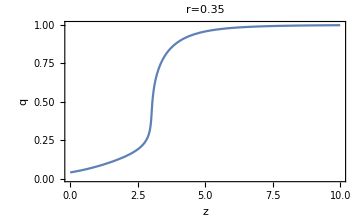

```mathematica
Show[%113,ImageSize->{360,215},AspectRatio->Full]
```

```mathematica
Export["/home/user/Desktop/MP_doc_templates/figures/one_layer_qv_r035.eps",%114,"EPS"]
```

/home/user/Desktop/MP_doc_templates/figures/one_layer_qv_r035.eps

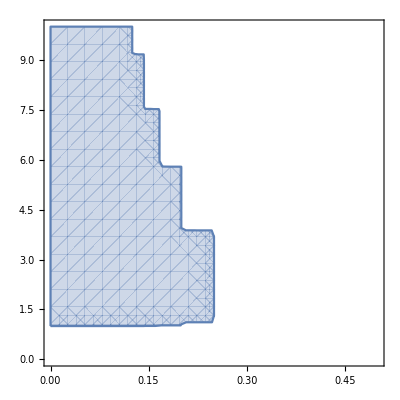

```mathematica
RegionPlot[G[0.001, z, r]>0.001,{r,0,0.5},{z,0,10}]
```

```mathematica
ContourPlot[CountRoots[Ggauss[q, z, r]-q, {q, 0, 1}] == 1,{r,0,0.5},{z,1,10}]
```

$Aborted

CountRoots::nuniv: -q+G[q,Charting`Private`pvar$19826,Charting`Private`pvar$19825] is not a univariate function of q.

CountRoots::nuniv: -q+G[q,1.00064,0.0000357143] is not a univariate function of q.

CountRoots::nuniv: -1. q+G[q,1.00064,0.0000357143] is not a univariate function of q.

General::stop: Further output of CountRoots::nuniv will be suppressed during this calculation.

-Graphics-

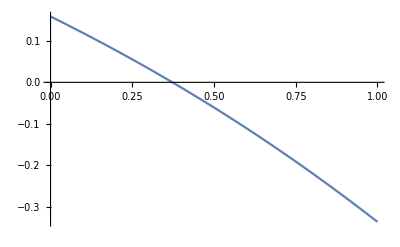

```mathematica
Plot[Ggauss[q, 1, 0.2] - q, {q, 0, 1}]
```

```mathematica
Gderiv[q_, z_, r_] = D[G[q,z, r], q]
```

ⅇ^-z z (-Boole[0>2 r]+Boole[1>2 r])+1/2 ⅇ^-z z^2 (1)+95+1/915100+(ⅇ^-z z^99 (-99 (1-q)^98 Boole[0>100 r]+294+99 q^98 Boole[99>100 r]))/(93326215443944152681699238856266700490715968264381621468593982862536979208272237582511852109168640000000000000000000000)
 |  |  |  |

```mathematica
CountRoots[x^2 + 1, {x,-1, 1}]
```

0

$Aborted

```mathematica
CountRoots[Ggauss[q, 4, 0.371]-q, {q, 0, 1}]
```

3

```mathematica
Cascade[z_, r_] = SeriesCoefficient[Series[Ggauss[q, z, r], {q, 0,1}],1];
```

```mathematica
Cascade2[z_, r_] = (SeriesCoefficient[Series[Ggauss[q,  z, r], {q, 0,2}],1]-1)^2 - 4*(SeriesCoefficient[Series[Ggauss[q,  z, r], {q, 0,2}],0]*SeriesCoefficient[Series[Ggauss[q, z, r], {q, 0,2}],2]);
```

```mathematica
Cascade[5, 0.4]
```

0.514593

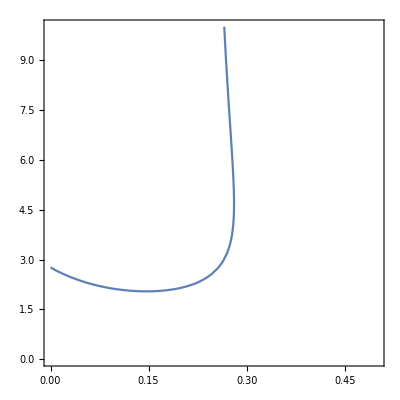

```mathematica
ContourPlot[Cascade[z, r]== 1, {r, 0, 0.5}, {z,0,10}]
```

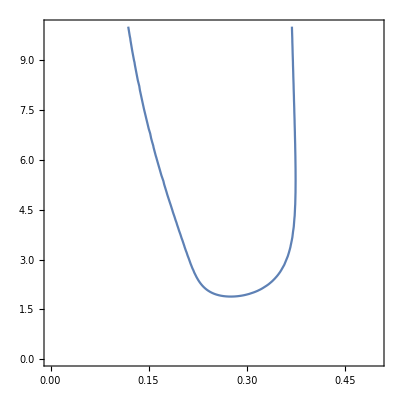

```mathematica
ContourPlot[Cascade2[z, r]== 0, {r, 0, 0.5}, {z,0,10}]
```

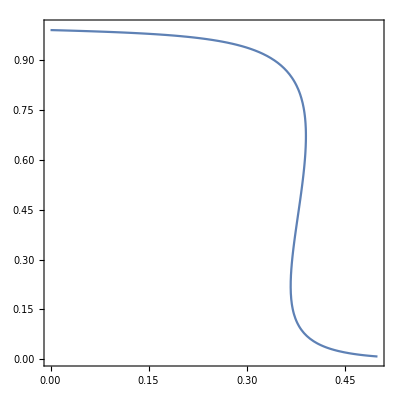

```mathematica
ContourPlot[Ggauss[q, 4,r]==q ,  {r, 0, 0.5},{q, 0, 1}, MaxRecursion->4]
```

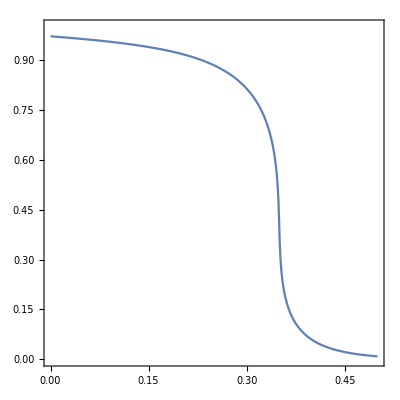

```mathematica
ContourPlot[Ggauss[q, 3,r]==q ,  {r, 0, 0.5},{q, 0, 1}, MaxRecursion->4]
```

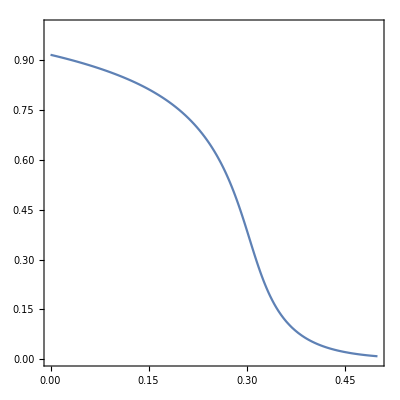

```mathematica
ContourPlot[Ggauss[q, 2,r]==q ,  {r, 0, 0.5},{q, 0, 1}, MaxRecursion->4]
```

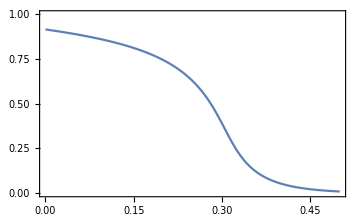

```mathematica
Show[%116,ImageSize->{360,215},AspectRatio->Full]
```

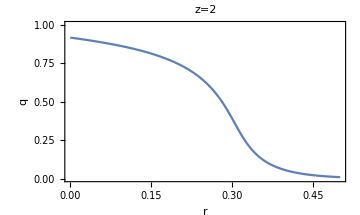

```mathematica
Show[%119,FrameLabel->{{HoldForm[q],None},{HoldForm[r],None}},PlotLabel->HoldForm[z=2],LabelStyle->{GrayLevel[0]}]
```

```mathematica
Export["/home/user/Desktop/MP_doc_templates/figures/one_layer_qr_z2.eps",%120,"EPS"]
```

/home/user/Desktop/MP_doc_templates/figures/one_layer_qr_z2.eps

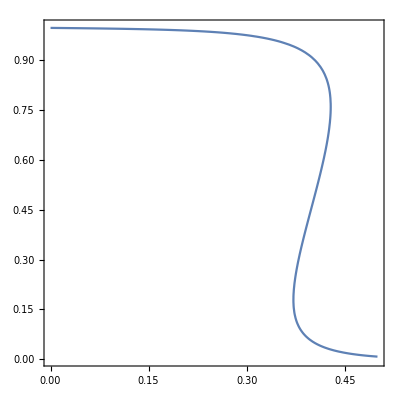

```mathematica
ContourPlot[Ggauss[q, 5,r]==q ,  {r, 0, 0.5},{q, 0, 1}, MaxRecursion->4]
```

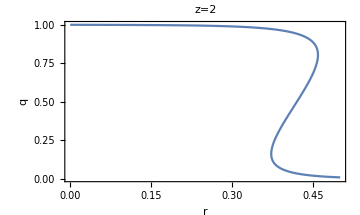

```mathematica
ContourPlot[Ggauss[q, 6,r]==q ,  {r, 0, 0.5},{q, 0, 1}, MaxRecursion->4, FrameLabel->{{HoldForm[q],None},{HoldForm[r],None}},PlotLabel->HoldForm[z=6],LabelStyle->{GrayLevel[0]}, ImageSize->{360, 215}, AspectRatio->Full]
```

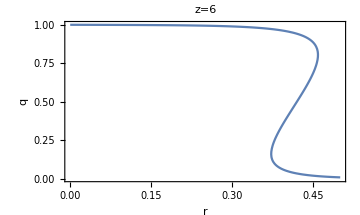

```mathematica
Show[%122, PlotLabel->HoldForm[z=6]]
```

```mathematica
Export["/home/user/Desktop/MP_doc_templates/figures/one_layer_qr_z6.eps",%124,"EPS"]
```

/home/user/Desktop/MP_doc_templates/figures/one_layer_qr_z6.eps

```mathematica
Export["/home/user/Desktop/MP_doc_templates/figures/one_layer_qr_z6.eps",%122,"EPS"]
```

/home/user/Desktop/MP_doc_templates/figures/one_layer_qr_z6.eps

```mathematica
Table[FindRoot[Ggauss[q, 2, r]-q, {q, 1}],{r,0,0.5,0.02}]
```

{{q→0.915424},{q→0.905762},{q→0.895221},{q→0.88366},{q→0.870884},{q→0.856631},{q→0.840541},{q→0.822118},{q→0.800676},{q→0.775244},{q→0.744418},{q→0.706106},{q→0.657087},{q→0.592326},{q→0.504587},{q→0.389481},{q→0.267082},{q→0.174144},{q→0.114888},{q→0.0775538},{q→0.0533317},{q→0.0371545},{q→0.0261081},{q→0.0184441},{q→0.0130674},{q→0.00926729}}

```mathematica
q/.%77
```

{0.915424,0.905762,0.895221,0.88366,0.870884,0.856631,0.840541,0.822118,0.800676,0.775244,0.744418,0.706106,0.657087,0.592326,0.504587,0.389481,0.267082,0.174144,0.114888,0.0775538,0.0533317,0.0371545,0.0261081,0.0184441,0.0130674,0.00926729}

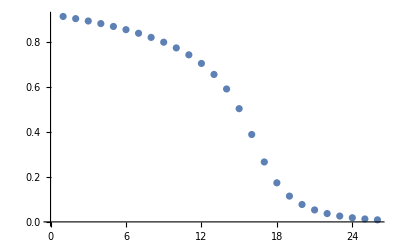

```mathematica
ListPlot[%78]
```

```mathematica
Apply[ρ [0, q_, 2, r_], %77]
```

0.937077

```mathematica
Table[FindRoot[Ggauss[q, 5, r]-q, {q, 0}],{r,0,0.42,0.02}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

{{q→-0.573525},{q→-0.818964},{q→0.995432},{q→0.994961},{q→0.994435},{q→0.99384},{q→0.993156},{q→0.992358},{q→0.991411},{q→0.990272},{q→0.988882},{q→0.987165},{q→0.98502},{q→0.982308},{q→0.978839},{q→0.0407124},{q→0.0810264},{q→0.120061},{q→0.157885},{q→0.0972039},{q→0.0543286},{q→0.0349895}}

```mathematica
q/.%84
```

{0.996253,0.99586,0.995432,0.994961,0.994435,0.99384,0.993156,0.992358,0.991411,0.990272,0.988882,0.987165,0.98502,0.982308,0.978839,0.97434,0.968407,0.960412,0.949296,0.933056,0.907039,0.853468}

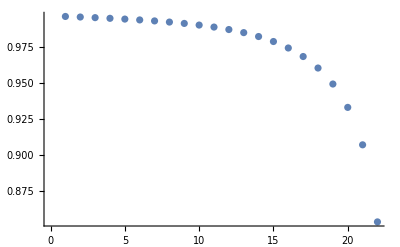

```mathematica
ListPlot[%87]
```

```mathematica
Show[%99]
```

-Graphics-

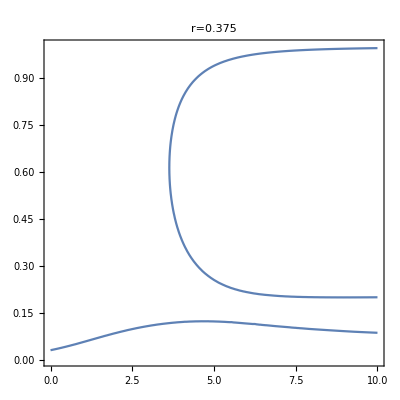

```mathematica
Show[%101,PlotLabel->HoldForm[r=0.375],LabelStyle->{GrayLevel[0]}]
```